```mathematica
$PlotTheme="Scientific"
```

Scientific

## Toy Model

We define the series

```mathematica
SN[NN_] := Sum[1/(n+1)(9/10)^n,{n,1,NN}]
```

The actual value of the series is

```mathematica
S = SN[∞]
```

1/9 (-9+10 Log[10])

Numerical value

```mathematica
N[S,4]
```

1.558

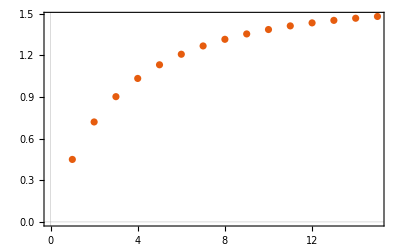

```mathematica
ListPlot[Table[SN[NN],{NN,1,15}]]
```

We assume N=15 is the max cut-off we can obtain. The largest three cut-offed sums we can compute are

```mathematica
Print[SN[15]," ~ ", N[SN[15],4]]
Print[SN[14]," ~ ", N[SN[14],4]]
Print[SN[13]," ~ ", N[SN[13],4]]
```

23703901684627396833/16016000000000000000 ~ 1.48

183576598917192603/125125000000000000 ~ 1.467

29066926903451937/20020000000000000 ~ 1.452

```mathematica
N[100*(1-SN[15]/S),2]
```

5.

Where the last value  1.480 is 5% away from the series value.

The coefficients aN are given by

```mathematica
aN[n_]:= 1/(n+1)(9/10)^n
```

And the ratios

```mathematica
cN[NN_]:= aN[NN]/aN[NN-1]
```

```mathematica
ratios=Table[{NN,cN[NN]},{NN,1,15}]
```

{{1,9/20},{2,3/5},{3,27/40},{4,18/25},{5,3/4},{6,27/35},{7,63/80},{8,4/5},{9,81/100},{10,9/11},{11,33/40},{12,54/65},{13,117/140},{14,21/25},{15,27/32}}

```mathematica
fit=Fit[ratios,{1,x^(-1),x^(-2)},x]
```

0.889228+0.303113/x^2-0.741398/x

```mathematica
L= Limit[fit,x->∞]
```

0.889228

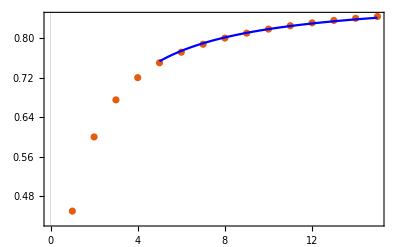

```mathematica
Show[ListPlot[ratios],Plot[fit,{x,5,15},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(SN[15]SN[13]-SN[14]^2)/(SN[15]-2SN[14]+SN[13])
```

3877629001570595709/2502500000000000000

```mathematica
N[LB,4]
```

1.55

```mathematica
N[100*(1-LB/S),1]
```

0.6

only 0.6% away from the value of the series.

The estimate for the upper bound is given by

```mathematica
UB=(SN[15] - L SN[14])/(1-L)
```

1.58331

```mathematica
N[UB,4]
```

1.58331

```mathematica
N[100*(UB/S-1),1]
```

1.59687

only 1.6% away from the value of the series.

## Boundary spins j = 1 and γ = 1.2

We import the CSV data into the appropriate columns

```mathematica
ROOTDIR = NotebookDirectory[];
```

```mathematica
{Ai0,Ai1,Ai2}=Transpose[Import[ROOTDIR<>"Delta_4_ampls/Immirzi_1.2/j_1.0/CSV_format/Delta_4_ampls_Dl_max_25.csv","Table"]];
```

### Boundary intertwiners i = 2

```mathematica
Ai2
```

{2.02191×10^-37,1.09032×10^-36,2.03264×10^-36,2.59232×10^-36,2.90128×10^-36,3.08743×10^-36,3.20956×10^-36,3.29512×10^-36,3.35803×10^-36,3.4058×10^-36,3.44301×10^-36,3.47247×10^-36,3.49617×10^-36,3.51544×10^-36,3.53128×10^-36,3.54445×10^-36,3.55549×10^-36,3.56483×10^-36,3.5728×10^-36,3.57966×10^-36,3.58559×10^-36,3.59077×10^-36,3.59531×10^-36,3.59931×10^-36,3.60286×10^-36,3.60603×10^-36}

```mathematica
ai2n[DL_]:=If[DL==0, Ai2[[1]],Ai2[[DL+1]]-Ai2[[DL]]]
```

```mathematica
ci2n[DL_]:=ai2n[DL]/ai2n[DL-1]
```

```mathematica
ratios=Table[{DL,ci2n[DL]},{DL,1,25}]
```

{{1,4.3925},{2,1.06103},{3,0.593934},{4,0.552037},{5,0.602494},{6,0.656083},{7,0.700583},{8,0.735289},{9,0.759268},{10,0.778946},{11,0.792019},{12,0.803943},{13,0.813385},{14,0.822347},{15,0.830821},{16,0.838484},{17,0.846313},{18,0.853041},{19,0.86004},{20,0.865917},{21,0.871983},{22,0.877093},{23,0.882257},{24,0.886704},{25,0.891073}}

```mathematica
fit=Fit[ratios[[5;;]],{1,x^(-1),x^(-2)},x]
```

0.962847+0.84655/x^2-1.96573/x

```mathematica
L= Limit[fit,x->∞]
```

0.962847

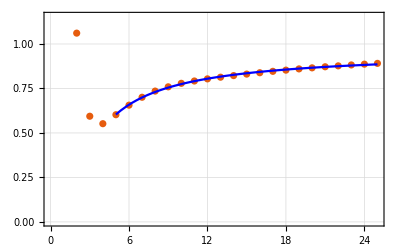

```mathematica
Show[ListPlot[ratios,GridLines->Automatic],Plot[fit,{x,5,25},PlotStyle->Blue]]
```

The lower bound approximation is given by

```mathematica
LB=(Ai2[[-1]]Ai2[[-3]]-Ai2[[-2]]^2)/(Ai2[[-1]]-2Ai2[[-2]]+Ai2[[-3]])
```

3.63191×10^-36

The estimate for the upper bound is given by

```mathematica
UB=(Ai2[[-1]] - L Ai2[[-2]])/(1-L)
```

3.68804×10^-36

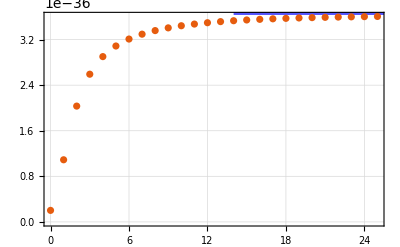

```mathematica
Ai2plot=ListPlot[Transpose[{Range[0,25],Ai2}],GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

```mathematica
Export[ROOTDIR<>"Plots/Plotg12j1i2.svg",Ai2plot]
```

/home/pdona/Dropbox/Ongoing Projects/HowToSpinFoamAmplitude/HowToSpinFoamAmplitude/Plots/Plotg12j1i2.svg

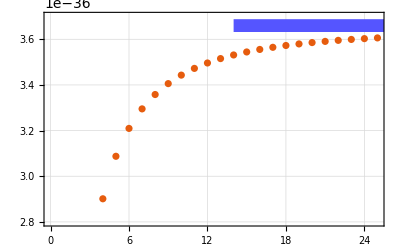

```mathematica
ListPlot[Transpose[{Range[4,25],Ai2[[5;;]]}],PlotRange->{Automatic,{2.8 10^(-36),3.7 10^(-36)}},GridLines->Automatic,Epilog->{Lighter@Blue,Rectangle[{14,LB},{26,UB}]}]
```

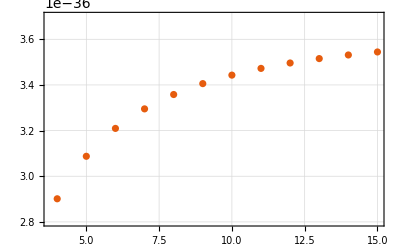

```mathematica
ListPlot[Transpose[{Range[4,15],Ai2[[5;;16]]}],PlotRange->{Automatic,{2.8 10^(-36),3.7 10^(-36)}},GridLines->Automatic]
```